Monte Carlo verification of results generated by parameters - al.txt with lambda = 0.9, kappa = 0.5, CI=0.

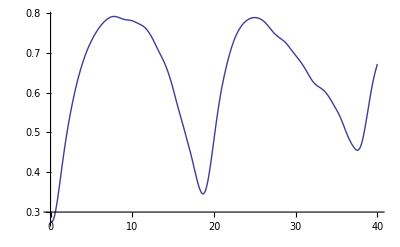

```mathematica
gamma={{0,1,0},{1,0,0},{0,0,0}};
omega={0,0,-1};
p={x[t],y[t],z[t]};
equ=D[p,t]-0.5(Cross[omega,p]+0.9(1+.5(p.gamma.p)^2)((gamma.p-(p.gamma.p)p)));
a11[t_]=0;
Do[
{r=RandomReal[NormalDistribution[0,1],3];
r=r/Norm[r];
solve=NDSolve[{equ[[1]]==0,equ[[2]]==0,equ[[3]]==0,x[0]==r[[1]],y[0]==r[[2]],z[0]==r[[3]]},p,{t,0,40}];
a11[t_]=a11[t]+(x[t]x[t]/.solve[[1]]);
},{n,1,100}]
Plot[a11[t]/100,{t,0,40}]
```